# Second attempt at Using NDSolve on Rate Equations

## We start by defining our rate equations. For Mathematica syntax, everything must be a function of [t]. Also, K is reserved and A does not seem to work, so these are replaced with Kin[t] and Ada[t]

```mathematica
rateEqns = {L'[t]==kb1*AKL[t]+kcat7*APLp[t]+kb1*LK[t]+kb1*LpAKL[t]+kcat7*LpAPLp[t]+kcat7*LpP[t]-ka1*AK[t]*L[t]-ka1*Kin[t]*L[t]-ka1*DF*L[t]*LpAK[t],Lp'[t]==kb7*APLp[t]+kcat1*AKL[t]+kcat1*LK[t]+kb2*LpA[t]+kb2*LpAK[t]+kb2*LpAKL[t]+kb2*LpAP[t]+kcat1*LpAKL[t]+kb2*LpAPLp[t]+kb7*LpAPLp[t]+kb7*LpP[t]-ka2*Ada[t]*Lp[t]-ka2*AK[t]*Lp[t]-ka2*AP[t]*Lp[t]-ka7*AP[t]*Lp[t]-ka7*Lp[t]*P[t]-ka2*DF*AKL[t]*Lp[t]-ka2*DF*APLp[t]*Lp[t]-ka7*DF*Lp[t]*LpAP[t],Kin'[t]==kb1*LK[t]+kb3*AK[t]+kcat1*LK[t]+kb3*LpAK[t]-ka3*Ada[t]*Kin[t]-ka1*Kin[t]*L[t]-ka3*Kin[t]*LpA[t],P'[t]==kb4*AP[t]+kb4*LpAP[t]+kb7*LpP[t]+kcat7*LpP[t]-ka4*Ada[t]*P[t]-ka7*Lp[t]*P[t]-ka4*LpA[t]*P[t],Ada'[t]==kb2*LpA[t]+kb3*AK[t]+kb3*AKL[t]+kb4*AP[t]+kb4*APLp[t]-ka2*Ada[t]*Lp[t]-ka3*Ada[t]*Kin[t]-ka3*Ada[t]*LK[t]-ka4*Ada[t]*LpP[t]-ka4*Ada[t]*P[t],LpA'[t]==kb3*LpAK[t]+kb3*LpAKL[t]+kb4*LpAP[t]+kb4*LpAPLp[t]+ka2*Ada[t]*Lp[t]-kb2*LpA[t]-ka3*Kin[t]*LpA[t]-ka4*LpA[t]*P[t]-ka3*DF*LK[t]*LpA[t]-ka4*DF*LpA[t]*LpP[t],LK'[t]==kb3*AKL[t]+kb3*LpAKL[t]+ka1*Kin[t]*L[t]-kb1*LK[t]-kcat1*LK[t]-ka3*Ada[t]*LK[t]-ka3*DF*LK[t]*LpA[t],LpP'[t]==kb4*APLp[t]+kb4*LpAPLp[t]+ka7*Lp[t]*P[t]-kb7*LpP[t]-kcat7*LpP[t]-ka4*Ada[t]*LpP[t]-ka4*DF*LpA[t]*LpP[t],LpAK'[t]==kb1*LpAKL[t]+kcat1*LpAKL[t]+ka2*AK[t]*Lp[t]+ka3*Kin[t]*LpA[t]-kb2*LpAK[t]-kb3*LpAK[t]-ka1*DF*L[t]*LpAK[t],LpAP'[t]==kb7*LpAPLp[t]+kcat7*LpAPLp[t]+ka2*AP[t]*Lp[t]+ka4*LpA[t]*P[t]-kb2*LpAP[t]-kb4*LpAP[t]-ka7*DF*Lp[t]*LpAP[t],LpAKL'[t]==ka1*DF*L[t]*LpAK[t]+ka2*DF*AKL[t]*Lp[t]+ka3*DF*LK[t]*LpA[t]-kb1*LpAKL[t]-kb2*LpAKL[t]-kb3*LpAKL[t]-kcat1*LpAKL[t],LpAPLp'[t]==ka2*DF*APLp[t]*Lp[t]+ka7*DF*Lp[t]*LpAP[t]+ka4*DF*LpA[t]*LpP[t]-kb2*LpAPLp[t]-kb4*LpAPLp[t]-kb7*LpAPLp[t]-kcat7*LpAPLp[t],AK'[t]==kb1*AKL[t]+kb2*LpAK[t]+kcat1*AKL[t]+ka3*Ada[t]*Kin[t]-kb3*AK[t]-ka1*AK[t]*L[t]-ka2*AK[t]*Lp[t],AP'[t]==kb2*LpAP[t]+kb7*APLp[t]+kcat7*APLp[t]+ka4*Ada[t]*P[t]-kb4*AP[t]-ka2*AP[t]*Lp[t]-ka7*AP[t]*Lp[t],AKL'[t]==kb2*LpAKL[t]+ka3*Ada[t]*LK[t]+ka1*AK[t]*L[t]-kb1*AKL[t]-kb3*AKL[t]-kcat1*AKL[t]-ka2*DF*AKL[t]*Lp[t],APLp'[t]==kb2*LpAPLp[t]+ka7*AP[t]*Lp[t]+ka4*Ada[t]*LpP[t]-kb4*APLp[t]-kb7*APLp[t]-kcat7*APLp[t]-ka2*DF*APLp[t]*Lp[t]}
```

{L'[t]==kb1 AKL[t]+kcat7 APLp[t]-ka1 AK[t] L[t]-ka1 Kin[t] L[t]+kb1 LK[t]-DF ka1 L[t] LpAK[t]+kb1 LpAKL[t]+kcat7 LpAPLp[t]+kcat7 LpP[t],Lp'[t]==kcat1 AKL[t]+kb7 APLp[t]+kcat1 LK[t]-ka2 Ada[t] Lp[t]-ka2 AK[t] Lp[t]-DF ka2 AKL[t] Lp[t]-ka2 AP[t] Lp[t]-ka7 AP[t] Lp[t]-DF ka2 APLp[t] Lp[t]+kb2 LpA[t]+kb2 LpAK[t]+kb2 LpAKL[t]+kcat1 LpAKL[t]+kb2 LpAP[t]-DF ka7 Lp[t] LpAP[t]+kb2 LpAPLp[t]+kb7 LpAPLp[t]+kb7 LpP[t]-ka7 Lp[t] P[t],Kin'[t]==kb3 AK[t]-ka3 Ada[t] Kin[t]-ka1 Kin[t] L[t]+kb1 LK[t]+kcat1 LK[t]-ka3 Kin[t] LpA[t]+kb3 LpAK[t],P'[t]==kb4 AP[t]+kb4 LpAP[t]+kb7 LpP[t]+kcat7 LpP[t]-ka4 Ada[t] P[t]-ka7 Lp[t] P[t]-ka4 LpA[t] P[t],Ada'[t]==kb3 AK[t]+kb3 AKL[t]+kb4 AP[t]+kb4 APLp[t]-ka3 Ada[t] Kin[t]-ka3 Ada[t] LK[t]-ka2 Ada[t] Lp[t]+kb2 LpA[t]-ka4 Ada[t] LpP[t]-ka4 Ada[t] P[t],LpA'[t]==ka2 Ada[t] Lp[t]-kb2 LpA[t]-ka3 Kin[t] LpA[t]-DF ka3 LK[t] LpA[t]+kb3 LpAK[t]+kb3 LpAKL[t]+kb4 LpAP[t]+kb4 LpAPLp[t]-DF ka4 LpA[t] LpP[t]-ka4 LpA[t] P[t],LK'[t]==kb3 AKL[t]+ka1 Kin[t] L[t]-kb1 LK[t]-kcat1 LK[t]-ka3 Ada[t] LK[t]-DF ka3 LK[t] LpA[t]+kb3 LpAKL[t],LpP'[t]==kb4 APLp[t]+kb4 LpAPLp[t]-kb7 LpP[t]-kcat7 LpP[t]-ka4 Ada[t] LpP[t]-DF ka4 LpA[t] LpP[t]+ka7 Lp[t] P[t],LpAK'[t]==ka2 AK[t] Lp[t]+ka3 Kin[t] LpA[t]-kb2 LpAK[t]-kb3 LpAK[t]-DF ka1 L[t] LpAK[t]+kb1 LpAKL[t]+kcat1 LpAKL[t],LpAP'[t]==ka2 AP[t] Lp[t]-kb2 LpAP[t]-kb4 LpAP[t]-DF ka7 Lp[t] LpAP[t]+kb7 LpAPLp[t]+kcat7 LpAPLp[t]+ka4 LpA[t] P[t],LpAKL'[t]==DF ka2 AKL[t] Lp[t]+DF ka3 LK[t] LpA[t]+DF ka1 L[t] LpAK[t]-kb1 LpAKL[t]-kb2 LpAKL[t]-kb3 LpAKL[t]-kcat1 LpAKL[t],LpAPLp'[t]==DF ka2 APLp[t] Lp[t]+DF ka7 Lp[t] LpAP[t]-kb2 LpAPLp[t]-kb4 LpAPLp[t]-kb7 LpAPLp[t]-kcat7 LpAPLp[t]+DF ka4 LpA[t] LpP[t],AK'[t]==-kb3 AK[t]+kb1 AKL[t]+kcat1 AKL[t]+ka3 Ada[t] Kin[t]-ka1 AK[t] L[t]-ka2 AK[t] Lp[t]+kb2 LpAK[t],AP'[t]==-kb4 AP[t]+kb7 APLp[t]+kcat7 APLp[t]-ka2 AP[t] Lp[t]-ka7 AP[t] Lp[t]+kb2 LpAP[t]+ka4 Ada[t] P[t],AKL'[t]==-kb1 AKL[t]-kb3 AKL[t]-kcat1 AKL[t]+ka1 AK[t] L[t]+ka3 Ada[t] LK[t]-DF ka2 AKL[t] Lp[t]+kb2 LpAKL[t],APLp'[t]==-kb4 APLp[t]-kb7 APLp[t]-kcat7 APLp[t]+ka7 AP[t] Lp[t]-DF ka2 APLp[t] Lp[t]+kb2 LpAPLp[t]+ka4 Ada[t] LpP[t]}

## We now define the values for the parameters that I will be testing on and substitute them in. These parameters are known to be oscillatory from Julia DifferentialEquations.

```mathematica
parameters = {ka1->1.001107643323893,kb1->281.14082293412173,kcat1->0.251,ka2->2.0300503992293732,kb2->0.9954105411980301,ka3->0.19893600692804198,kb3->0.24254011544624787,ka4->0.001,kb4->0.001,ka7->2.768126898343966,kb7->0.14464903871512103,kcat7->0.5821403067955622,DF->14185.701046371441}
```

{ka1→1.00111,kb1→281.141,kcat1→0.251,ka2→2.03005,kb2→0.995411,ka3→0.198936,kb3→0.24254,ka4→0.001,kb4→0.001,ka7→2.76813,kb7→0.144649,kcat7→0.58214,DF→14185.7}

```mathematica
rateEqnWithParams = rateEqns /. parameters
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]-1.00111 AK[t] L[t]-1.00111 Kin[t] L[t]+281.141 LK[t]-14201.4 L[t] LpAK[t]+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==0.251 AKL[t]+0.144649 APLp[t]+0.251 LK[t]-2.03005 Ada[t] Lp[t]-2.03005 AK[t] Lp[t]-28797.7 AKL[t] Lp[t]-4.79818 AP[t] Lp[t]-28797.7 APLp[t] Lp[t]+0.995411 LpA[t]+0.995411 LpAK[t]+1.24641 LpAKL[t]+0.995411 LpAP[t]-39267.8 Lp[t] LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]-2.76813 Lp[t] P[t],Kin'[t]==0.24254 AK[t]-0.198936 Ada[t] Kin[t]-1.00111 Kin[t] L[t]+281.392 LK[t]-0.198936 Kin[t] LpA[t]+0.24254 LpAK[t],P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]-0.001 Ada[t] P[t]-2.76813 Lp[t] P[t]-0.001 LpA[t] P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]-0.198936 Ada[t] Kin[t]-0.198936 Ada[t] LK[t]-2.03005 Ada[t] Lp[t]+0.995411 LpA[t]-0.001 Ada[t] LpP[t]-0.001 Ada[t] P[t],LpA'[t]==2.03005 Ada[t] Lp[t]-0.995411 LpA[t]-0.198936 Kin[t] LpA[t]-2822.05 LK[t] LpA[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]-14.1857 LpA[t] LpP[t]-0.001 LpA[t] P[t],LK'[t]==0.24254 AKL[t]+1.00111 Kin[t] L[t]-281.392 LK[t]-0.198936 Ada[t] LK[t]-2822.05 LK[t] LpA[t]+0.24254 LpAKL[t],LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]-0.726789 LpP[t]-0.001 Ada[t] LpP[t]-14.1857 LpA[t] LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]-1.23795 LpAK[t]-14201.4 L[t] LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]-0.996411 LpAP[t]-39267.8 Lp[t] LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+2822.05 LK[t] LpA[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==-0.24254 AK[t]+281.392 AKL[t]+0.198936 Ada[t] Kin[t]-1.00111 AK[t] L[t]-2.03005 AK[t] Lp[t]+0.995411 LpAK[t],AP'[t]==-0.001 AP[t]+0.726789 APLp[t]-4.79818 AP[t] Lp[t]+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==-281.634 AKL[t]+1.00111 AK[t] L[t]+0.198936 Ada[t] LK[t]-28797.7 AKL[t] Lp[t]+0.995411 LpAKL[t],APLp'[t]==-0.727789 APLp[t]+2.76813 AP[t] Lp[t]-28797.7 APLp[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

## We now define our initial conditions (from same oscillatory solution as parameters)

```mathematica
initialU={L[0]==3.0,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.0,Lp[0]==0.0,LpA[0]==0.0,LK[0]==0.0,LpP[0]==0.0,LpAK[0]==0.0,LpAP[0]==0.0,LpAKL[0]==0.0,LpAPLp[0]==0.0,AK[0]==0.0,AP[0]==0.0,AKL[0]==0.0,APLp[0]==0.0}
```

{L[0]==3.,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.,Lp[0]==0.,LpA[0]==0.,LK[0]==0.,LpP[0]==0.,LpAK[0]==0.,LpAP[0]==0.,LpAKL[0]==0.,LpAPLp[0]==0.,AK[0]==0.,AP[0]==0.,AKL[0]==0.,APLp[0]==0.}

## I think we need the following import to be able to successfully use NDSolve

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

## We now can call the NDSolve function.

```mathematica
plot1 = NDSolve[{rateEqnWithParams,initialU},{L},{t,0,500},DependentVariables->{L,Kin,P,Ada,Lp,LpA,LK,LpP,LpAK,LpAP,LpAKL,LpAPLp,AK,AP,AKL,APLp}]
```

{{L→InterpolatingFunction[…]}}

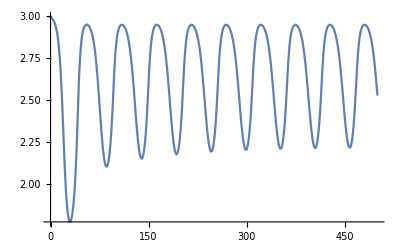

```mathematica
Plot[Evaluate[L[t]/.plot1],{t,0,500},PlotRange->All]
```

## Ok, let’s now start eliminating variables now that we know we can do NDSolve. We’ll start with LK

```mathematica
rateEqnWithParams=FullSimplify[rateEqnWithParams]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+281.141 LK[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==0.251 LK[t]+APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+281.392 LK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t],P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-0.198936 LK[t]-2.03005 Lp[t]-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]-2822.05 LK[t]-14.1857 LpP[t]-0.001 P[t]),LK'[t]==0.24254 AKL[t]+1.00111 Kin[t] L[t]+LK[t] (-281.392-0.198936 Ada[t]-2822.05 LpA[t])+0.24254 LpAKL[t],LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+2822.05 LK[t] LpA[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+0.198936 Ada[t] LK[t]+AKL[t] (-281.634-28797.7 Lp[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
rateEqnWithParams = rateEqnWithParams /.LK'[t]->0
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+281.141 LK[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==0.251 LK[t]+APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+281.392 LK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t],P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-0.198936 LK[t]-2.03005 Lp[t]-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]-2822.05 LK[t]-14.1857 LpP[t]-0.001 P[t]),0==0.24254 AKL[t]+1.00111 Kin[t] L[t]+LK[t] (-281.392-0.198936 Ada[t]-2822.05 LpA[t])+0.24254 LpAKL[t],LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+2822.05 LK[t] LpA[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+0.198936 Ada[t] LK[t]+AKL[t] (-281.634-28797.7 Lp[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
LKsub = Solve[rateEqnWithParams[[7]],LK[t]]
```

{{LK[t]→-(1. (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])}}

```mathematica
NoLK = Delete[rateEqnWithParams,7]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+281.141 LK[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==0.251 LK[t]+APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+281.392 LK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t],P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-0.198936 LK[t]-2.03005 Lp[t]-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]-2822.05 LK[t]-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+2822.05 LK[t] LpA[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+0.198936 Ada[t] LK[t]+AKL[t] (-281.634-28797.7 Lp[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoLK=FullSimplify[NoLK]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+281.141 LK[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==0.251 LK[t]+APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+281.392 LK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t],P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-0.198936 LK[t]-2.03005 Lp[t]-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]-2822.05 LK[t]-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+2822.05 LK[t] LpA[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+0.198936 Ada[t] LK[t]+AKL[t] (-281.634-28797.7 Lp[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoLK=NoLK/.LKsub
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])-(281.141 (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])+281.141 LpAKL[t]+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]-(0.251 (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t]-(281.392 (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(0.198936 (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(2822.05 (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+14201.4 L[t] LpAK[t]-(2822.05 LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])-(0.198936 Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(-281.392-0.198936 Ada[t]-2822.05 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLK=Simplify[NoLK]
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t]+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+14201.4 L[t] LpAK[t]-282.63 LpAKL[t]+(3440.6 LpA[t] (1. AKL[t]+4.1276 Kin[t] L[t]+1. LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+0.995411 LpAKL[t]+(0.24254 Ada[t] (1. AKL[t]+4.1276 Kin[t] L[t]+1. LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t]),APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLK=FullSimplify[NoLK]
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t]+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAK'[t]==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+14201.4 L[t] LpAK[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLKU = Delete[initialU, 7]
```

{L[0]==3.,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.,Lp[0]==0.,LpA[0]==0.,LpP[0]==0.,LpAK[0]==0.,LpAP[0]==0.,LpAKL[0]==0.,LpAPLp[0]==0.,AK[0]==0.,AP[0]==0.,AKL[0]==0.,APLp[0]==0.}

```mathematica
plot2 = NDSolve[{NoLK,NoLKU},{L},{t,0,500},DependentVariables->{L,Kin,P,Ada,Lp,LpA,LpP,LpAK,LpAP,LpAKL,LpAPLp,AK,AP,AKL,APLp}]
```

{{L→InterpolatingFunction[…]}}

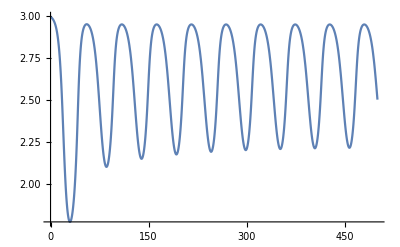

```mathematica
Plot[Evaluate[L[t]/.plot2],{t,0,500},PlotRange->All]
```

## We successfully eliminated LK. We will continue the process: set variable to 0, solve for variable, substitute in, simplify, fullsimplify, solve, plot. We continue with LpAK.

```mathematica
NoLpAK=NoLK/.LpAK'[t]->0
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t]+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],0==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+14201.4 L[t] LpAK[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
LpAKSub=FullSimplify[Solve[NoLpAK[[1]][[8]], LpAK[t]]]
```

{{LpAK[t]→(0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t])/(0.0000871709+1. L[t])}}

```mathematica
NoLpAK=NoLpAK[[1]]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-14201.4 LpAK[t])+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+0.995411 LpAK[t]+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+0.24254 LpAK[t]+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+0.24254 LpAK[t]+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],0==2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+(-1.23795-14201.4 L[t]) LpAK[t]+281.392 LpAKL[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+14201.4 L[t] LpAK[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+0.995411 LpAK[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoLpAK=Delete[NoLpAK,8]/.LpAKSub
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]-(14201.4 (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t]))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.995411 (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(0.24254 (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(0.24254 (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(14201.4 L[t] (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t])+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t],LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+(0.995411 (0.000142947 AK[t] Lp[t]+0.0000140082 Kin[t] LpA[t]+0.0198144 LpAKL[t]))/(0.0000871709+1. L[t]),AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLpAK=Simplify[NoLpAK]
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]+(-2.03005 AK[t] Lp[t]-0.198936 Kin[t] LpA[t]-281.392 LpAKL[t])/(0.0000871709+1. L[t]))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(2.03005 L[t] (1. AK[t] Lp[t]+0.0979956 Kin[t] LpA[t]+138.613 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t]),AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLpAK=FullSimplify[NoLpAK]
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]+(-2.03005 AK[t] Lp[t]-0.198936 Kin[t] LpA[t]-281.392 LpAKL[t])/(0.0000871709+1. L[t]))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AK'[t]==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t]),AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoLpAKU=Delete[NoLKU,8]
```

{L[0]==3.,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.,Lp[0]==0.,LpA[0]==0.,LpP[0]==0.,LpAP[0]==0.,LpAKL[0]==0.,LpAPLp[0]==0.,AK[0]==0.,AP[0]==0.,AKL[0]==0.,APLp[0]==0.}

```mathematica
plot3=NDSolve[{NoLpAK,NoLpAKU},{L},{t,0,500},DependentVariables->{L,Kin,P,Ada,Lp,LpA,LpP,LpAP,LpAKL,LpAPLp,AK,AP,AKL,APLp}]
```

{{L→InterpolatingFunction[…]}}

```mathematica
Plot[Evaluate[L[t]/.plot2],{t,0,500},PlotRange->All]
```

-Graphics-

## We continue now to eliminate AK

```mathematica
NoAK=NoLpAK/.AK'[t]->0
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]+(-2.03005 AK[t] Lp[t]-0.198936 Kin[t] LpA[t]-281.392 LpAKL[t])/(0.0000871709+1. L[t]))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],0==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t]),AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoAK=NoAK[[1]]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 AK[t]-1.00111 Kin[t]+(-2.03005 AK[t] Lp[t]-0.198936 Kin[t] LpA[t]-281.392 LpAKL[t])/(0.0000871709+1. L[t]))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-2.03005 AK[t]-4.79818 AP[t]-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==0.24254 AK[t]+Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AK[t]+0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(0.0000346704 AK[t] Lp[t]+3.39755×10^-6 Kin[t] LpA[t]+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (2.03005 AK[t] Lp[t]+0.198936 Kin[t] LpA[t]+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],0==281.392 AKL[t]+0.198936 Ada[t] Kin[t]+AK[t] (-0.24254-1.00111 L[t]-2.03005 Lp[t])+(0.000142291 AK[t] Lp[t]+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t])/(0.0000871709+1. L[t]),AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==1.00111 AK[t] L[t]+AKL[t] (-281.634-28797.7 Lp[t])+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
AKSub=FullSimplify[Solve[NoAK[[-4]],AK[t]]]
```

{{AK[t]→(Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t])/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))}}

```mathematica
NoAK=Delete[NoAK,-4]/.AKSub
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]-(2.03005 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])-(1.00111 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(0.000142291 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-4.79818 AP[t]-(2.03005 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(3.39755×10^-6 Kin[t] LpA[t]+(0.0000346704 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(0.24254 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+(0.24254 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(0.0000346704 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(2.03005 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(1.00111 L[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}}

```mathematica
NoAK=Simplify[NoAK[[1]]]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]-(2.03005 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])-(1.00111 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(0.000142291 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-4.79818 AP[t]-(2.03005 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(3.39755×10^-6 Kin[t] LpA[t]+(0.0000346704 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(0.24254 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+(0.24254 (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(0.0000346704 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(2.03005 Lp[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(1.00111 L[t] (Ada[t] Kin[t] (0.0000173223+0.198716 L[t])+AKL[t] (0.0245021+281.08 L[t])+0.0000139285 Kin[t] LpA[t]+0.0197016 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoAK=FullSimplify[NoAK]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-4.79818 AP[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AP'[t]==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoAKU=Delete[NoLpAKU,-4]
```

{L[0]==3.,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.,Lp[0]==0.,LpA[0]==0.,LpP[0]==0.,LpAP[0]==0.,LpAKL[0]==0.,LpAPLp[0]==0.,AP[0]==0.,AKL[0]==0.,APLp[0]==0.}

```mathematica
plot4=NDSolve[{NoAK,NoAKU},{L},{t,0,500},DependentVariables->{L,Kin,P,Ada,Lp,LpA,LpP,LpAP,LpAKL,LpAPLp,AP,AKL,APLp},Method->{"IndexReduction"->Automatic}]
```

{{L→InterpolatingFunction[…]}}

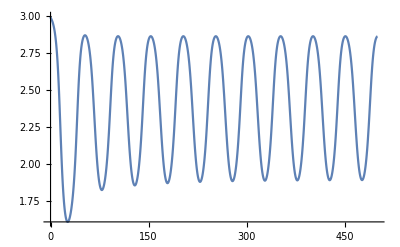

```mathematica
Plot[Evaluate[L[t]/.plot4],{t,0,500},PlotRange->All]
```

## We move on to eliminate AP

```mathematica
NoAP = NoAK/.AP'[t]->0.
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-4.79818 AP[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],0.==0.726789 APLp[t]+AP[t] (-0.001-4.79818 Lp[t])+0.995411 LpAP[t]+0.001 Ada[t] P[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
APSub = FullSimplify[Solve[NoAP[[-3]],AP[t]]]
```

{{AP[t]→(0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t])/(-0.001-4.79818 Lp[t])}}

```mathematica
NoAP=Delete[NoAP,-3]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]-4.79818 AP[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 AP[t]+0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t],Ada'[t]==0.24254 AKL[t]+0.001 AP[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==2.03005 AP[t] Lp[t]+(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t],LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+2.76813 AP[t] Lp[t]+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]}

```mathematica
NoAP=NoAP/.APSub
```

{{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]-(4.79818 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t]+(0.001 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),Ada'[t]==0.24254 AKL[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t])+(0.001 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t]+(2.03005 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]+(2.76813 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])}}

```mathematica
NoAP=NoAP[[1]]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]-(4.79818 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t]+(0.001 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),Ada'[t]==0.24254 AKL[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t])+(0.001 (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t]+(2.03005 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]+(2.76813 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])}

```mathematica
NoAP=Simplify[NoAP]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]+(0.+3.48726 APLp[t]+4.77616 LpAP[t]+0.00479818 Ada[t] P[t])/(-0.001-4.79818 Lp[t])),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t]+(0.-0.000726789 APLp[t]-0.000995411 LpAP[t]-1.×10^-6 Ada[t] P[t])/(-0.001-4.79818 Lp[t]),Ada'[t]==0.24254 AKL[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t])+(0.-0.000726789 APLp[t]-0.000995411 LpAP[t]-1.×10^-6 Ada[t] P[t])/(-0.001-4.79818 Lp[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t]+(2.03005 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]+(2.76813 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])}

```mathematica
NoAP=FullSimplify[NoAP]
```

{L'[t]==281.141 AKL[t]+0.58214 APLp[t]+L[t] (-1.00111 Kin[t]+(-0.198936 Kin[t] LpA[t]+(Lp[t] (AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-281.392 LpAKL[t])/(0.0000871709+1. L[t])+(AKL[t] (-0.0120964-138.767 L[t])+Ada[t] Kin[t] (-8.55183×10^-6-0.0981041 L[t])-6.87635×10^-6 Kin[t] LpA[t]-0.00972649 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t])))+281.141 LpAKL[t]+(342.763 AKL[t]+1414.79 Kin[t] L[t]+342.763 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.58214 LpAPLp[t]+0.58214 LpP[t],Lp'[t]==APLp[t] (0.144649-28797.7 Lp[t])+AKL[t] (0.251-28797.7 Lp[t])+0.995411 LpA[t]+(0.0000139439 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (1.2155×10^-9+0.0000139439 L[t])+AKL[t] (1.71931×10^-6+0.0197234 L[t])+9.7736×10^-10 Kin[t] LpA[t]+1.38246×10^-6 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.0197234 LpAKL[t])/(0.0000871709+1. L[t])+(0.306016 AKL[t]+1.26311 Kin[t] L[t]+0.306016 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])+1.24641 LpAKL[t]+0.995411 LpAP[t]+1.14006 LpAPLp[t]+0.144649 LpP[t]+Lp[t] (-2.03005 Ada[t]+(AKL[t] (-0.0245292-281.392 L[t])+Ada[t] Kin[t] (-0.0000173414-0.198936 L[t])-0.0000139439 Kin[t] LpA[t]-0.0197234 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))-39267.8 LpAP[t]-2.76813 P[t]+(0.+3.48726 APLp[t]+4.77616 LpAP[t]+0.00479818 Ada[t] P[t])/(-0.001-4.79818 Lp[t])),Kin'[t]==Kin[t] (-0.198936 Ada[t]-1.00111 L[t]-0.198936 LpA[t])+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+(343.069 AKL[t]+1416.05 Kin[t] L[t]+343.069 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t]),P'[t]==0.001 LpAP[t]+0.726789 LpP[t]+(-0.001 Ada[t]-2.76813 Lp[t]-0.001 LpA[t]) P[t]+(0.-0.000726789 APLp[t]-0.000995411 LpAP[t]-1.×10^-6 Ada[t] P[t])/(-0.001-4.79818 Lp[t]),Ada'[t]==0.24254 AKL[t]+0.001 APLp[t]+0.995411 LpA[t]+(Ada[t] Kin[t] (2.07187×10^-6+0.0237679 L[t])+AKL[t] (0.00293062+33.6193 L[t])+1.66595×10^-6 Kin[t] LpA[t]+0.00235645 LpAKL[t])/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+Ada[t] (-0.198936 Kin[t]-2.03005 Lp[t]+(-0.24254 AKL[t]-1.00111 Kin[t] L[t]-0.24254 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-0.001 LpP[t]-0.001 P[t])+(0.-0.000726789 APLp[t]-0.000995411 LpAP[t]-1.×10^-6 Ada[t] P[t])/(-0.001-4.79818 Lp[t]),LpA'[t]==2.03005 Ada[t] Lp[t]+(3.39755×10^-6 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (2.96167×10^-10+3.39755×10^-6 L[t])+AKL[t] (4.18924×10^-7+0.00480578 L[t])+2.38142×10^-10 Kin[t] LpA[t]+3.36848×10^-7 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+0.00480578 LpAKL[t])/(0.0000871709+1. L[t])+0.24254 LpAKL[t]+0.001 LpAP[t]+0.001 LpAPLp[t]+LpA[t] (-0.995411-0.198936 Kin[t]+(-3440.6 AKL[t]-14201.4 Kin[t] L[t]-3440.6 LpAKL[t])/(1414.48+1. Ada[t]+14185.7 LpA[t])-14.1857 LpP[t]-0.001 P[t]),LpP'[t]==0.001 APLp[t]+0.001 LpAPLp[t]+(-0.726789-0.001 Ada[t]-14.1857 LpA[t]) LpP[t]+2.76813 Lp[t] P[t],LpAP'[t]==(-0.996411-39267.8 Lp[t]) LpAP[t]+0.726789 LpAPLp[t]+0.001 LpA[t] P[t]+(2.03005 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t]),LpAKL'[t]==28797.7 AKL[t] Lp[t]+(LpA[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(0.099712+0.0000704935 Ada[t]+1. LpA[t])-282.63 LpAKL[t]+(L[t] (0.198936 Kin[t] LpA[t]+(Lp[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000104147+0.0000170786 Lp[t]+L[t] (0.119518+0.493144 L[t]+1. Lp[t]))+281.392 LpAKL[t]))/(0.0000871709+1. L[t]),LpAPLp'[t]==28797.7 APLp[t] Lp[t]+39267.8 Lp[t] LpAP[t]-1.7232 LpAPLp[t]+14.1857 LpA[t] LpP[t],AKL'[t]==AKL[t] (-281.634-28797.7 Lp[t])+(L[t] (Ada[t] Kin[t] (0.0000173414+0.198936 L[t])+AKL[t] (0.0245292+281.392 L[t])+0.0000139439 Kin[t] LpA[t]+0.0197234 LpAKL[t]))/(0.0000211191+0.000034632 Lp[t]+L[t] (0.242359+1. L[t]+2.0278 Lp[t]))+(Ada[t] (0.24254 AKL[t]+1.00111 Kin[t] L[t]+0.24254 LpAKL[t]))/(1414.48+1. Ada[t]+14185.7 LpA[t])+0.995411 LpAKL[t],APLp'[t]==APLp[t] (-0.727789-28797.7 Lp[t])+0.995411 LpAPLp[t]+0.001 Ada[t] LpP[t]+(2.76813 Lp[t] (0.-0.726789 APLp[t]-0.995411 LpAP[t]-0.001 Ada[t] P[t]))/(-0.001-4.79818 Lp[t])}

```mathematica
NoAPU=Delete[NoAKU,-3]
```

{L[0]==3.,Kin[0]==0.5,P[0]==0.3,Ada[0]==2.,Lp[0]==0.,LpA[0]==0.,LpP[0]==0.,LpAP[0]==0.,LpAKL[0]==0.,LpAPLp[0]==0.,AKL[0]==0.,APLp[0]==0.}

```mathematica
plot5=NDSolve[{NoAP,NoAPU},{L},{t,0,500},DependentVariables->{L,Kin,P,Ada,Lp,LpA,LpP,LpAP,LpAKL,LpAPLp,AKL,APLp},Method->{"IndexReduction"->Automatic}]
```

{{L→InterpolatingFunction[…]}}

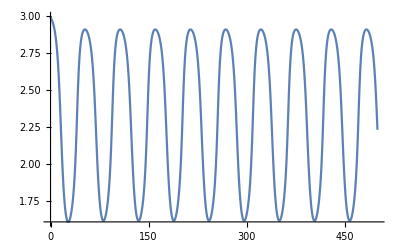

```mathematica
Plot[Evaluate[L[t]/.plot5],{t,0,500},PlotRange->All]
```

## We now will eliminate AKL